```mathematica
Gaussian[x_,s_]:=Exp[-x^2/(2s^2)]/(s*Sqrt[2*Pi])
```

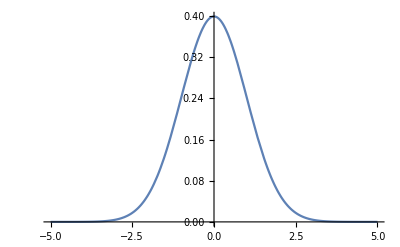

```mathematica
Plot[Gaussian[x,1],{x,-5,5}]
```

```mathematica
Integrate[Gaussian[x,s],{x,-Infinity,Infinity},Assumptions->s>0]
```

1

```mathematica
Decay[x_,tau_]:=UnitStep[x]*Exp[-x/tau]/tau
```

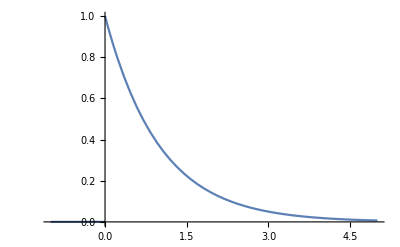

```mathematica
Plot[Decay[x,1],{x,-1,5}]
```

```mathematica
Integrate[Decay[x,tau],{x,-Infinity,Infinity},Assumptions->tau>0]
```

```mathematica
erfcx[x_]:=2/Sqrt[Pi]*HermiteH[-1,x]
```

```mathematica
P1[t_,τ_,σ_]:=Evaluate[Convolve[Decay[x,τ],Gaussian[x,σ],x,t]]
```

```mathematica
P2[t_,τ_,σ_]:=(ⅇ^((σ^2-2 t τ)/(2 τ^2)) (Erfc[(σ^2-t τ)/(√2 τ σ)]))/(2 τ)
```

```mathematica
P3[t_,τ_,σ_]:=(Exp[(σ^2-2 t τ)/(2 τ^2)-(σ/(√2 τ)-t/(√2 σ))^2] erfcx[σ/(√2 τ)-t/(√2 σ)])/(2 τ)
```

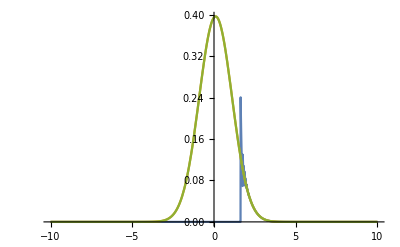

```mathematica
Plot[{P1[t,.1,1],P2[t,.1,1],P3[t,.1,1]},{t,-10,10},PlotRange->Full]
```

```mathematica
NIntegrate[P3[t,.01,20],{t,-50,200},MinRecursion->40,MaxRecursion->50,WorkingPrecision->20]
```

NIntegrate::precw: The precision of the argument function (56.419 ⅇ^(5000. (400-0.02 t)-(1414.21-1/20 Power[«2»] t)^2) HermiteH[-1,1414.21-t/(20 √2)]) is less than WorkingPrecision (20.).

0.99379908837298545506

```mathematica
FullSimplify[P[t,τ,σ],Assumptions->{σ>0,τ>0,t∈Reals}]
```

(ⅇ^((σ^2-2 t τ)/(2 τ^2)) (1+Erf[(-σ+(t τ)/σ)/(√2 τ)]))/(2 τ)

```mathematica
(ⅇ^((σ^2-2 t τ)/(2 τ^2)) (Erfc[(σ-(t τ)/σ)/(√2 τ)]))/(2 τ)//TeXForm
```

\frac{e^{\frac{\sigma ^2-2 t \tau }{2 \tau ^2}} \text{erfc}\left(\frac{\sigma -\frac{t
   \tau }{\sigma }}{\sqrt{2} \tau }\right)}{2 \tau }

True

```mathematica
Convolve[P[t,τ,σ],P[t,τ,σ],t,x]
```

Convolve[ⅇ^((σ^2-2 t τ)/(2 τ^2)) (1+Erf[(√(1/σ^2) (-σ^2+t τ))/(√2 τ)]),ⅇ^((σ^2-2 t τ)/(2 τ^2)) (1+Erf[(√(1/σ^2) (-σ^2+t τ))/(√2 τ)]),t,x]/(4 τ^2)

```mathematica
Limit[P[t,τ,σ],τ->0]
```

$Aborted

```mathematica
K[t_,τ_,σ_]:=Integrate[P2[T,τ,σ]*P2[t-T,τ,σ],{T,-Infinity,Infinity},Assumptions->{t∈Reals,τ>0,σ>0}]
```

```mathematica
FullSimplify[P2[T,τ,σ]*P2[t+T,τ,σ],Assumptions->{t∈Reals,τ>0,σ>0}]
```

(ⅇ^((σ^2-(t+2 T) τ)/τ^2) Erfc[(σ^2-T τ)/(√2 σ τ)] Erfc[(σ^2-(t+T) τ)/(√2 σ τ)])/(4 τ^2)

```mathematica
K[t_,τ_,σ_]:=NIntegrate[(ⅇ^((σ^2-(t+2 T) τ)/τ^2) Erfc[(σ^2-T τ)/(√2 σ τ)] Erfc[(σ^2-(t+T) τ)/(√2 σ τ)])/(4 τ^2),{T,-40,40},MinRecursion->2,MaxRecursion->20]
```

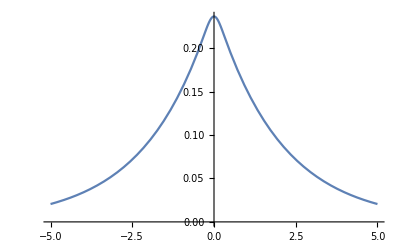

```mathematica
Plot[K[t,2,.1],{t,-5,5}]
```

```mathematica
∫_-20^20 (ⅇ^(1/2 (1-2 (1-T))-(1/(√2)-(1-T)/(√2))^2+1/2 (1-2 T)-(1/(√2)-T/(√2))^2) HermiteH[-1,1/(√2)-(1-T)/(√2)] HermiteH[-1,1/(√2)-T/(√2)])/π ⅆT//N
```

```mathematica
K[0,1,1]
```

0.213792

```mathematica
NIntegrate[K[t,1,1],{t,-20,20}]
```

NIntegrate::inumr: The integrand 1/4 ⅇ^(1-t-2 T) Erfc[(1-T)/(√2)] Erfc[(1-t-T)/(√2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-40.,-20.}}.

NIntegrate::inumr: The integrand 1/4 ⅇ^(1+t-2 T) Erfc[(1-T)/(√2)] Erfc[(1+t-T)/(√2)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{-40.,-20.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

1.

```mathematica
NIntegrate[P[t,0.1,10],{t,-Infinity,Infinity}]
```

1.

```mathematica
P[t,τ_,σ_]:=(ⅇ^((σ^2-2 t τ)/(2 τ^2)) (Erfc[(σ-(t τ)/σ)/(√2 τ)]))/(2 τ)
```

```mathematica
Integrate[P[t,σ,τ],{t,-Infinity,Infinity},Assumptions->{σ>0,τ>0}]
```

1

```mathematica
NIntegrate[P[t,1,1],{t,-Infinity,Infinity}]
```

1.

```mathematica
erfcx[x_]:=If[x>5*10^7,1/(x Sqrt[π]),Exp[x^2] Erfc[x]]
```

```mathematica
P2[0.1,0.1,1]//N
```

0.39699

```mathematica
P2[t,τ,σ]
```

(ⅇ^((σ^2-2 t τ)/(2 τ^2)-(σ-(t τ)/σ)^2/(2 τ^2)) If[(σ-(t τ)/σ)/(√2 τ)>50000000,1/(((σ-(t τ)/σ) √π)/(√2 τ)),Exp[((σ-(t τ)/σ)/(√2 τ))^2] Erfc[(σ-(t τ)/σ)/(√2 τ)]])/(2 τ)

```mathematica
Plot[P2[t,0.1,1]]
```

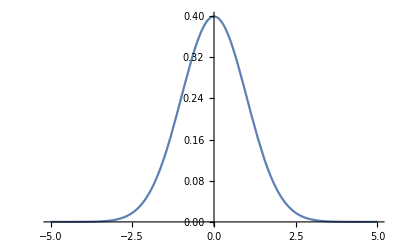

```mathematica
Plot[P2[t,0.001,1],{t,-5,5}]
```

```mathematica
NIntegrate[P2[t,1,1],{t,-Infinity,100}]
```

2.4803×10^-8

```mathematica
erfcx[-10]//N
```

5.37623×10^43

```mathematica
Erfc[-1000]//N
```

2.

```mathematica
erfcx[1000000]//N
```

5.64×10^-7

```mathematica
f[1000000]//N
```

5.6419×10^-7

```mathematica
f[t_,σ_,τ_]:=(σ^2-2 t τ)/(2 τ^2)-((σ-(t τ)/σ)/(√2 τ))
```

```mathematica
f[-100,1,1]//N
```

29.0822

```mathematica
FullSimplify[P1[t,τ,σ]==P2[t,τ,σ],Assumptions->σ>0]
```

True

```mathematica
FullSimplify[P2[t,τ,σ]==P1[t,τ,σ]]
```

(ⅇ^((σ^2-2 t τ)/(2 τ^2)) (-1+√(1/σ^2) σ))/τ==0

```mathematica
FullSimplify[P1[t,τ,σ]]
```

(ⅇ^((σ^2-2 t τ)/(2 τ^2)) (1+Erf[(-σ^2+t τ)/(√2 σ τ)]))/(2 τ)

```mathematica
f[x_]/;x≥0:=2/Sqrt[Pi]*HermiteH[-1,x]
```

```mathematica
f[1]//N
```

0.427584

```mathematica
g[-1]//N
```

```mathematica
t[σ_,τ_]:=NIntegrate[(ⅇ^((σ^2-(t+2 T) τ)/τ^2) Erfc[(σ^2-T τ)/(√2 σ τ)] Erfc[(σ^2-(t+T) τ)/(√2 σ τ)])/(4 τ^2),{T,-10-20*(σ+τ),10+20*(σ+τ)},{t,-10-20*(σ+τ),10+20*(σ+τ)},WorkingPrecision->10,MinRecursion->10,MaxRecursion->30]
```

```mathematica
Parallelize@LogLogPlot[t[τ,1],{τ,0.1,10},PlotPoints->5]
```

Parallelize::nopar1: LogLogPlot[t[τ,1],{τ,0.1,10},PlotPoints→5] cannot be parallelized; proceeding with sequential evaluation.

$Aborted

```mathematica
tab=ParallelTable[{10^τ,t[10^τ,1]},{τ,-2,2,.1}]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon
     will be suppressed during this calculation.

{{0.01,0.9968885458},{0.0125893,0.9992747867},{0.0158489,1.000021754},{0.0199526,1.000026747},{0.0251189,0.9999304112},{0.0316228,0.999986329},{0.0398107,0.9999990575},{0.0501187,0.9999989154},{0.0630957,0.9999512725},{0.0794328,0.9999939198},{0.1,0.999987495},{0.125893,0.9999969732},{0.158489,0.9999996233},{0.199526,1.000000117},{0.251189,1.000000344},{0.316228,1.000004764},{0.398107,1.000002127},{0.501187,0.9999975371},{0.630957,0.9999987437},{0.794328,1.000003532},{1.,0.9998886653},{1.25893,0.9999968524},{1.58489,1.000002347},{1.99526,1.000002772},{2.51189,1.000000184},{3.16228,1.000000077},{3.98107,0.9999994415},{5.01187,0.9999949624},{6.30957,0.9999995173},{7.94328,0.9999993643},{10.,0.9999996575},{12.5893,0.9999997466},{15.8489,0.999999882},{19.9526,0.9999996081},{25.1189,0.9999995796},{31.6228,0.9999995974},{39.8107,0.9999997009},{50.1187,1.000000239},{63.0957,0.9999997537},{79.4328,0.999999744},{100.,0.9999998106}}

```mathematica
x=Table[10^x,{x,-2,1,.05}]
```

{0.01,0.0112202,0.0125893,0.0141254,0.0158489,0.0177828,0.0199526,0.0223872,0.0251189,0.0281838,0.0316228,0.0354813,0.0398107,0.0446684,0.0501187,0.0562341,0.0630957,0.0707946,0.0794328,0.0891251,0.1,0.112202,0.125893,0.141254,0.158489,0.177828,0.199526,0.223872,0.251189,0.281838,0.316228,0.354813,0.398107,0.446684,0.501187,0.562341,0.630957,0.707946,0.794328,0.891251,1.,1.12202,1.25893,1.41254,1.58489,1.77828,1.99526,2.23872,2.51189,2.81838,3.16228,3.54813,3.98107,4.46684,5.01187,5.62341,6.30957,7.07946,7.94328,8.91251,10.}

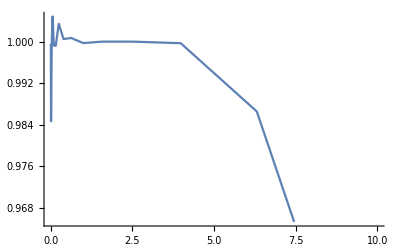

```mathematica
ListLinePlot[tab]
```

```mathematica
ParallelTable[ListLinePlot[KSmoothTest[RandomReal[{-10,10},10],9]],{j,1,2}]
```

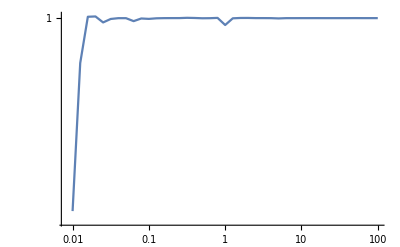

```mathematica
ListLogLogPlot[tab,Joined->True]
```

```mathematica
monitorParallelTable[,{τ,0.1,100,0.1}]
```

```mathematica
SetAttributes[monitorParallelTable,HoldAll]
monitorParallelTable[expr_,iter__List,updatethreshold_]:=Module[{counter=1,thresh=updatethreshold},SetSharedVariable[counter];
ParallelEvaluate[localcounter=1;];
Monitor[ParallelTable[If[localcounter≥thresh,counter=counter+localcounter;localcounter=1,localcounter++];expr,iter],counter]]
```

NIntegrate::slwcon: 
   Numerical integration converging too slowly; suspect one of the following:
    singularity, value of the integration is 0, highly oscillatory integrand,
    or WorkingPrecision too small.

$Aborted

```mathematica
tab2=ParallelTable[{τ,m[τ,1]},{τ,0.05,10,.05}]
```

{{0.05,0.498842414},{0.1,0.4956770306},{0.15,0.4909505014},{0.2,0.4849924559},{0.25,0.4780765816},{0.3,0.4704444647},{0.35,0.462281942},{0.4,0.4537438265},{0.45,0.444954456},{0.5,0.4360167135},{0.55,0.4270119802},{0.6,0.4180063826},{0.65,0.4090466417},{0.7,0.4001926436},{0.75,0.3914571448},{0.8,0.3828759488},{0.85,0.3744662055},{0.9,0.3662439526},{0.95,0.3582193274},{1.,0.3503972843},{1.05,0.3427828645},{1.1,0.3353790207},{1.15,0.3281853888},{1.2,0.3212010151},{1.25,0.314423687},{1.3,0.3078507164},{1.35,0.3014770302},{1.4,0.2952987573},{1.45,0.2893111459},{1.5,0.2835088009},{1.55,0.2778877664},{1.6,0.272440254},{1.65,0.2671621143},{1.7,0.2620473502},{1.75,0.257090757},{1.8,0.2522869171},{1.85,0.2476302969},{1.9,0.2431161509},{1.95,0.2387391752},{2.,0.2344943965},{2.05,0.2303770274},{2.1,0.2263823994},{2.15,0.2225060508},{2.2,0.218743632},{2.25,0.215090959},{2.3,0.2115439768},{2.35,0.2080987817},{2.4,0.204759624},{2.45,0.2014990249},{2.5,0.1983373685},{2.55,0.1952630672},{2.6,0.1922736308},{2.65,0.1893656958},{2.7,0.1865367102},{2.75,0.1837824277},{2.8,0.1811018192},{2.85,0.1784915044},{2.9,0.1759493636},{2.95,0.1734717773},{3.,0.1710582393},{3.05,0.1687059669},{3.1,0.1664125536},{3.15,0.164176046},{3.2,0.1619945763},{3.25,0.1598660934},{3.3,0.1577894036},{3.35,0.155762034},{3.4,0.1537828956},{3.45,0.1518502477},{3.5,0.1499630484},{3.55,0.148118875},{3.6,0.1463168066},{3.65,0.1445555466},{3.7,0.1428331401},{3.75,0.1411496718},{3.8,0.1395030253},{3.85,0.1378928104},{3.9,0.1363171743},{3.95,0.1347750052},{4.,0.1332659015},{4.05,0.1317888644},{4.1,0.1303423621},{4.15,0.1289255531},{4.2,0.1275380237},{4.25,0.126178476},{4.3,0.1248465484},{4.35,0.12354123},{4.4,0.1222617661},{4.45,0.1210075182},{4.5,0.1197776024},{4.55,0.1185715745},{4.6,0.1173884991},{4.65,0.1162279636},{4.7,0.1150892034},{4.75,0.1139717099},{4.8,0.1128749151},{4.85,0.1117976321},{4.9,0.1107406151},{4.95,0.1096870894},{5.,0.1086677018},{5.05,0.107666611},{5.1,0.1066985914},{5.15,0.1057323222},{5.2,0.1047828379},{5.25,0.1038498734},{5.3,0.102932712},{5.35,0.1020309731},{5.4,0.101127296},{5.45,0.1002734508},{5.5,0.0994162458},{5.55,0.09857322954},{5.6,0.09774399067},{5.65,0.09692820359},{5.7,0.09612555256},{5.75,0.0953357314},{5.8,0.09455844308},{5.85,0.09379351727},{5.9,0.09304043609},{5.95,0.09229904858},{6.,0.09156896459},{6.05,0.09085018598},{6.1,0.0901423399},{6.15,0.08944515799},{6.2,0.08875844007},{6.25,0.08808194527},{6.3,0.0874154768},{6.35,0.08675876918},{6.4,0.08611163822},{6.45,0.08547383677},{6.5,0.08484525935},{6.55,0.08422566073},{6.6,0.08361483946},{6.65,0.08301265066},{6.7,0.08241889841},{6.75,0.081833421},{6.8,0.08125593682},{6.85,0.08068647817},{6.9,0.08012490328},{6.95,0.0795708353},{7.,0.07902423464},{7.05,0.07848495414},{7.1,0.07795271626},{7.15,0.07742765099},{7.2,0.07690948655},{7.25,0.07639811707},{7.3,0.07589335988},{7.35,0.07539511409},{7.4,0.07490325762},{7.45,0.07440847931},{7.5,0.0739382353},{7.55,0.07346483806},{7.6,0.07299733539},{7.65,0.07253575216},{7.7,0.07207980959},{7.75,0.0716294746},{7.8,0.07118464597},{7.85,0.07074522485},{7.9,0.0703111147},{7.95,0.06988222124},{8.,0.06945845237},{8.05,0.06903971812},{8.1,0.06862593057},{8.15,0.06821689157},{8.2,0.06781274339},{8.25,0.06741328997},{8.3,0.06701845109},{8.35,0.06662816155},{8.4,0.06624232088},{8.45,0.06586082869},{8.5,0.06548368115},{8.55,0.06511077298},{8.6,0.06474203401},{8.65,0.0643773956},{8.7,0.06401679057},{8.75,0.0636601532},{8.8,0.06330741916},{8.85,0.06295852548},{8.9,0.06261341055},{8.95,0.06227201403},{9.,0.06193427683},{9.05,0.06160014114},{9.1,0.06126955029},{9.15,0.06094244882},{9.2,0.06061878239},{9.25,0.06029849777},{9.3,0.05998154282},{9.35,0.05966783706},{9.4,0.05935738891},{9.45,0.05906524974},{9.5,0.05874598647},{9.55,0.05844493026},{9.6,0.05814691551},{9.65,0.05785189354},{9.7,0.05755981994},{9.75,0.05727050891},{9.8,0.05698421154},{9.85,0.05670072501},{9.9,0.05642001769},{9.95,0.05614204931},{10.,0.05586678036}}

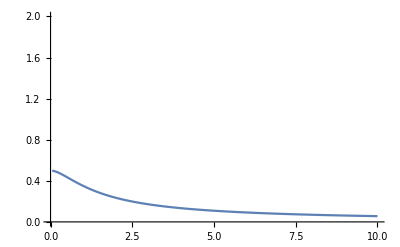

```mathematica
ListLinePlot[tab2,PlotRange->{{0,10},{0,2}}]
```

```mathematica
g[t_,τ_]=Exp[-Abs[t]/τ]
```

ⅇ^(-Abs[t]/τ)

```mathematica
m[σ_,τ_]:=NIntegrate[(ⅇ^((σ^2-(t+2 T) τ)/τ^2) Erfc[(σ^2-T τ)/(√2 σ τ)] Erfc[(σ^2-(t+T) τ)/(√2 σ τ)])/(4 τ^2)*Exp[-Abs[t]/τ],{T,-10-20*(σ+τ),10+20*(σ+τ)},{t,-10-20*(σ+τ),10+20*(σ+τ)},WorkingPrecision->10,MinRecursion->10,MaxRecursion->30]
```

```mathematica
m[1,10]
```

0.4956699099

```mathematica
tab3:=tab2
```

```mathematica
tab3
```

{{{0.01,0.0112202,0.0125893,0.0141254,0.0158489,0.0177828,0.0199526,0.0223872,46,5.01187,5.62341,6.30957,7.07946,7.94328,8.91251,10.},44},198,{1}}
 |  |  |  |

```mathematica
tab2[[All,2]]*=2;
```

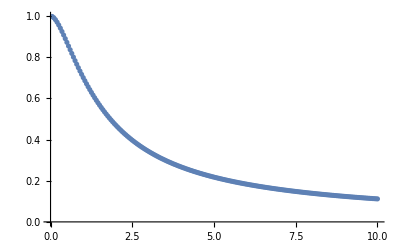

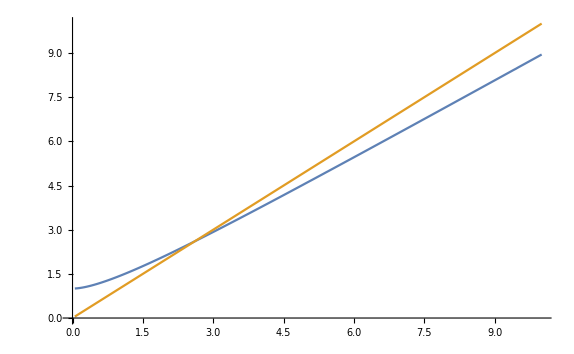

```mathematica
ListPlot[tab2]
```

```mathematica
lintab=Table[{τ,Max[1,τ]},{τ,0.05,10,.05}];
```

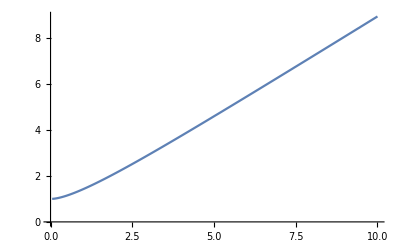

```mathematica
ListLinePlot[{{#1, 1/#2}&@@@tab2}]
```

```mathematica
Show[%400,AxesLabel->{HoldForm[σ/τ],HoldForm[M]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

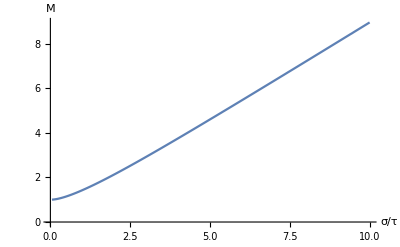

```mathematica
Max[1,0]
```

1